```mathematica
ClearAll[GraphPartion`CompareIsoperimetricAlgs]

SetDirectory[NotebookDirectory[]]
Import["GraphPartition.m"]
<< GraphPartition`
$Context
```

C:\Users\Chuqian\Desktop\research\graphPartitioning

Global`

```mathematica
Graphics3D[{Arrow[{{0,0,0},d}],Arrow[{{0,0,0},v}],Arrow[{{0,0,0},len*dd}],Line[{len*dd,v}]},Axes->True]
```

-Graphics3D-

```mathematica
sym=LineGraph[GridGraph[{10,10}]];
```

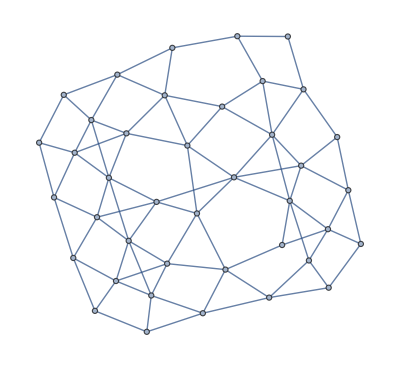

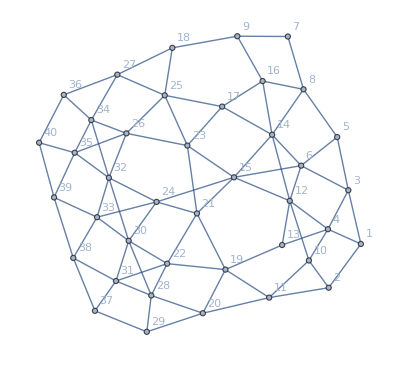

```mathematica
g = EdgeDelete[sym,EdgeList[sym][[RandomSample[Range[Length[EdgeList[sym]]],8]]]]
g=UndirectedGraph[#,VertexLabels->Automatic,VertexWeight->Table[1/V[#],V[#]], EdgeWeight->Automatic]&@g
```

```mathematica
basisVectors = FingerprintVectors[g,3]
```

{{0.301029,-0.504451,0.370264},{0.175933,-1.07388,1.32327},{0.376382,-0.255818,0.00127054},{0.326526,-0.144452,-0.226113},{0.433375,-0.200155,-0.0485922},{0.420354,-0.135017,-0.102836},{0.512072,-0.187169,-0.0337605},{0.479143,-0.17043,-0.056571},{0.520757,-0.164709,-0.0233099},{0.24166,0.0516696,0.426175},{0.0687023,1.51688,0.883962},{0.371233,-0.0526715,-0.288784},{0.318079,0.0782117,-1.65185},{0.453981,-0.109708,-0.103092},{0.442552,-0.0175344,-0.0873431},{0.492898,-0.145488,-0.0531987},{0.493464,-0.0979061,-0.0421816},{0.533055,-0.122272,0.0046695},{0.312248,0.542406,-0.0937561},{0.302689,0.700574,0.279993},{0.430295,0.167517,-0.0290986},{0.417229,0.288043,0.0358545},{0.48498,-0.0188804,-0.0245875},{0.470222,0.0827523,0.0119794},{0.51775,-0.0783491,-0.000207889},{0.516595,-0.0289306,0.0235339},{0.536412,-0.0845576,0.0251664},{0.409869,0.357302,0.133626},{0.395692,0.424903,0.183781},{0.460634,0.175508,0.0642425},{0.448855,0.23668,0.0918989},{0.502635,0.038672,0.0427446},{0.490747,0.0887978,0.0569917},{0.529121,-0.037046,0.039287},{0.524244,-0.00985023,0.0480732},{0.541475,-0.0613643,0.044557},{0.450272,0.256032,0.125363},{0.482024,0.145713,0.0880491},{0.513977,0.0405429,0.0655829},{0.534647,-0.0232903,0.0568577}}

```mathematica
iv = VectorPartition[basisVectors,V[g]/2, OptimizationOn->False,
				OptimizationObj-> (CriterionPartitionFunction[g,#,0.5]&)]
N[CriterionPartitionFunction[g,iv,0.5]]
dir=Normalize[Total[Table[basisVectors[[i]]*iv[[i]],{i,1,Length[iv]}]]]
```

{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,1,0,1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1}

40.

{0.854363,0.475786,0.209027}

```mathematica
(**)
ds=Table[
With[{iv=VectorMaxOnDirection[basisVectors,V[g]/2,{Cos[2*Pi/40*i],Sin[2*Pi/200*i]}, 
OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)]},
Total[Table[basisVectors[[i]]*iv[[i]],{i,1,Length[iv]}]]]
,{i,200}];
```

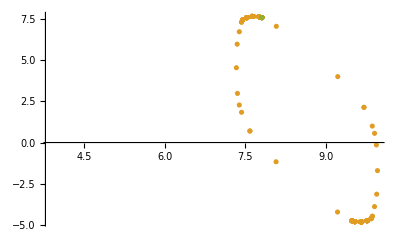

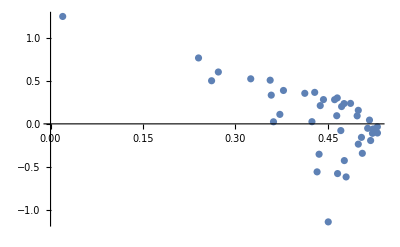

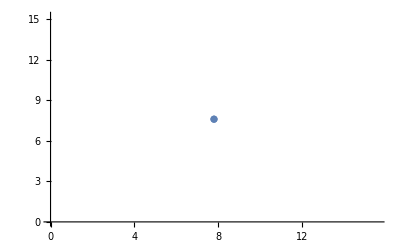

```mathematica
ListPlot[{basisVectors,ds,{Total[Table[basisVectors[[i]]*iv[[i]],{i,1,Length[iv]}]]}}]
ListPlot[basisVectors]
ListPlot[{Total[Table[basisVectors[[i]]*iv[[i]],{i,1,Length[iv]}]]}]
```

#### Idea - Mallow+Random Projection - KMeans + Linear combination of mean vectors?

```mathematica
Total[Table[basisVectors[[i]]*iv[[i]],{i,1,Length[iv]}]]
```

{7.80838,7.611}

```mathematica
basisVectors
```

{{0.542596,-0.500634},{0.528961,-0.648542},{0.541272,-0.352593},{0.532291,-0.504873},{0.541256,-0.2064},{0.523681,-0.20257},{0.535709,0.0134871},{0.533554,-0.0681414},{0.512601,0.0910108},{0.517436,-0.999927},{0.501588,-0.449169},{0.518022,-0.354568},{0.516869,-0.320746},{0.513972,-0.0900256},{0.478619,-0.0133699},{0.518017,0.00626795},{0.486677,0.0881232},{0.458814,0.249173},{0.475032,-0.106904},{0.45966,-0.0454067},{0.448781,0.103339},{0.422999,0.173361},{0.450478,0.170263},{0.391516,0.289239},{0.43898,0.261883},{0.37407,0.407233},{0.399598,0.390519},{0.4158,0.195523},{0.420957,0.174817},{0.376327,0.335636},{0.373794,0.335104},{0.343924,0.456576},{0.284665,0.559907},{0.347128,0.49267},{0.264576,0.650669},{0.328208,0.554246},{0.362149,0.370231},{0.266433,0.596666},{0.0198609,1.11732},{0.212636,0.775445}}

```mathematica
ds
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
(**)
newiv=VectorMaxOnDirection[basisVectors,V[g]/2,dir, 
OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)]
N[CriterionPartitionFunction[g,newiv,0.5]]
(*dir=Normalize[Total[Table[basisVectors[[i]]*newiv[[i]],{i,1,Length[iv]}]]]*)
```

{11,20,29,28,37,31,19,22,38,30,33,39,40,32,35,24,36,34,21,26,27,25,23,18,17,9,15,7,16,10,8,14,6,5,12,3,4,1,13,2}

{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,1,0,1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1}

40.

```mathematica
newiv=VectorPartition[basisVectors,V[g]/2, 
OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&),
Method->MallowProbe]
N[CriterionPartitionFunction[g,newiv,0.5]]
(*dir=Normalize[Total[Table[basisVectors[[i]]*newiv[[i]],{i,1,Length[iv]}]]]*)
```

{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,1,0,1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1}

40.

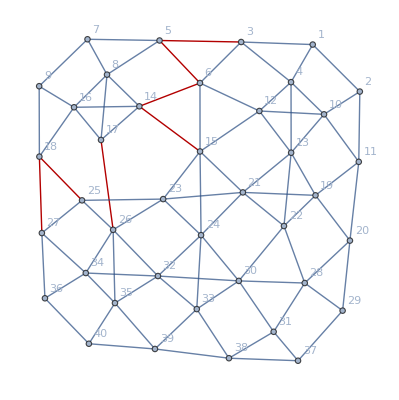

```mathematica
ShowSpectralCut[g]
```

```mathematica
Total[{1,2,3}]
```

6

```mathematica
labelledVectors = MapIndexed[ {#1, #2[[1]]}&, basisVectors];
		labelledVectors = SortBy[-labelledVectors, Dot[#[[1]],Normalize[dir]]&];
		partition = Map[#[[2]]&,Take[labelledVectors,eta]]
		Table[ If[MemberQ[partition,i], 1, 0], {i, Length[vectors]} ] 
		(*Table[ If[projectedLens[[i]]>0, 1, 0], {i, Length[vectors]}]*)
```

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{{{-0.549443,0.0520724},-2},{{-0.538277,-0.0808209},-29},{{-0.536101,-0.0974633},-37},«34»,{{-0.304097,0.705322},-9},{{-0.227927,1.14517},-16},{{-0.0352697,-1.27817},-17}},eta].

Part::partd: Part specification eta⟦2⟧ is longer than depth of object.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{{-0.538277,-0.0808209},-29},eta⟦2⟧].

Take[{{-0.538277,-0.0808209},-29},eta⟦2⟧]

{}

```mathematica
Map[#[[2]]&,Take[labelledVectors,3]]
```

{25,16,18}

```mathematica
N[SpectralEdges[g,IncludeObj->True]]
```

{36.8286,{9.<->18.,11.<->19.,11.<->20.,13.<->19.,15.<->21.,15.<->23.,15.<->24.,17.<->23.,17.<->25.}}

```mathematica
N[CriterionPartitionFunction[g,Table[1/V[g],V[g]],0.5]]
```

∞

```mathematica
p = Table[0,V[g]];
For[i=1,i<=V[g],i++,p[[i]]=1;N[CriterionPartitionFunction[g,p,0.5]]]
```

```mathematica
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
p
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
p = Table[0,V[g]];
Table[p[[i]]=1;N[CriterionPartitionFunction[g,p,0.5]],{i,1,V[g]}]
```

{123.077,84.2105,72.0721,66.6667,82.2857,70.5882,69.2641,62.5,63.0824,64.,60.1881,61.9048,59.2593,48.3516,42.6667,41.6667,49.1049,48.4848,52.1303,52.,52.1303,52.5253,57.289,58.3333,55.4667,57.1429,54.7009,61.9048,60.1881,64.,63.0824,68.75,69.2641,70.5882,73.1429,88.8889,86.4865,105.263,123.077,∞}

```mathematica
Take[{1,3,4},5]
```

Take::take: Cannot take positions 1 through 5 in {1,3,4}.

Take[{1,3,4},5]

```mathematica
ArgMin[{1,3,4}[[x]], {x,1,3}]
```

Part::pkspec1: The expression x cannot be used as a part specification.

ArgMin::ivar: 1 is not a valid variable.

```mathematica
ArgMin[{1,3,4}⟦x⟧,x]
```

Part::pkspec1: The expression x cannot be used as a part specification.

```mathematica
{obj, index}=Maximum[{1,3,4},Identity]
obj
index
```

{4,3}

4

3

```mathematica
Maximum[{1,3,4}]
```

Maximum[{1,3,4}]

```mathematica
Position
```

```mathematica
RandomReal[1,3]
```

{0.85257,0.252606,0.44045}